```mathematica
(*---GLOBAL CONSTANTS---*)tau0=41.9 (*Myr*);
alphaLock=1/3;
ngTheoretical=Sqrt[1+alphaLock]//N; (*1.1547*)

(*---ROBUST INGESTION FUNCTION---*)
importSPARC[path_String]:=Module[{raw,clean},raw=Import[path,"Table"];
(*Filter:Keep only rows where the first column is a number (strips headers)*)clean=Select[raw,NumberQ[First[#]]&];
(*Map to meaningful associations for readability*)Map[<|"R"->#[[1]],"vObs"->#[[2]],"errV"->#[[3]],"vGas"->#[[4]],"vDisk"->#[[5]],"vBulge"->#[[6]]|>&,clean]];

(*---LOAD SAMPLE DATASET---*)
(*Replace with your actual directory path*)
dir="C:/Users/Physics/SPARC/Data/";
galIDs={"NGC2403","UGC128","NGC3198"};
galaxyStore=AssociationThread[galIDs->(importSPARC[dir<>#<>".txt"]&/@galIDs)];
```

Import::nffil: File C:/Users/Physics/SPARC/Data/NGC2403.txt not found during Import.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,NumberQ[First[#1]]&].

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of NumberQ[First[#1]]& does not exist.

Part::partw: Part 3 of NumberQ[First[#1]]& does not exist.

Part::partw: Part 4 of NumberQ[First[#1]]& does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Import::nffil: File C:/Users/Physics/SPARC/Data/UGC128.txt not found during Import.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,NumberQ[First[#1]]&].

Import::nffil: File C:/Users/Physics/SPARC/Data/NGC3198.txt not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,NumberQ[First[#1]]&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

```mathematica
(*Sum baryonic components in quadrature (Newtonian Base)*)vNewtonian[pt_Association]:=Sqrt[pt["vGas"]^2+pt["vDisk"]^2+pt["vBulge"]^2];

(*Predict velocity based on ng (GRUT Boost)*)
vPredict[pt_Association,ng_]:=ng*vNewtonian[pt];

(*Calculate chi-square for a single galaxy*)
chiSqGal[galData_List,ng_]:=Total[Table[(pt["vObs"]-vPredict[pt,ng])^2/pt["errV"]^2,{pt,galData}]];
```

```mathematica
(*EFT Penalty:Steep wall if ng^2>2.0*)pEFT[ng_]:=10^6*UnitStep[ng^2-2.0]*(ng^2-2.0)^2;

(*Local Penalty:Anchors high-freq/local gravity to G (ng->1)*)
pLoc[ng_]:=10^5*(ng^2-1)^2;

(*Total Cost Functional*)
totalCost[ng_,weights_List]:=Module[{wEFT,wLoc,wCos},{wEFT,wLoc,wCos}=weights;
wEFT*pEFT[ng]+wLoc*pLoc[ng]+wCos*Total[chiSqGal[#,ng]&/@Values[galaxyStore]]];
```

```mathematica
(*1. Run the Minimizer for the Baseline Scenario*)baselineFit=FindMinimum[totalCost[n,{1,1,1}],{n,1.15}];

(*2. Generate the Likelihood Surface for Plotting*)
plotData=Table[{n,totalCost[n,{1,1,1}]},{n,1.0,1.3,0.005}];

(*3. Output Results*)
Print["Calculated Best Fit ng: ",n/. baselineFit[[2]]];
Print["Theoretical alpha-lock ng: ",ngTheoretical];
Print["Delta: ",(n/. baselineFit[[2]])-ngTheoretical];
```

FindMinimum::nrnum: The function value 10400.6+3 chiSqGal[<||>,1.15] is not a real number at {n} = {1.15}.

ReplaceAll::reps: {n,1.15} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Calculated Best Fit ng: n/.{n,1.15}

Theoretical alpha-lock ng: 1.1547

FindMinimum::nrnum: The function value 10400.6+3 chiSqGal[<||>,1.15] is not a real number at {n} = {1.15}.

ReplaceAll::reps: {n,1.15} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Delta: -1.1547+(n/.{n,1.15})

```mathematica
(*---STATISTICAL VERIFICATION---*)verifyClosure[fitValue_,theoreticalValue_]:=Module[{delta,sigmaTotal,dF,chiSqRed},delta=fitValue-theoreticalValue;
(*Degrees of Freedom=Total Data Points-1 (the single parameter ng)*)dF=Total[Length/@Values[galaxyStore]]-1;
(*Minimum Cost at the fit point*)chiSqRed=baselineFit[[1]]/dF;
Print["--- CLOSURE ANALYSIS ---"];
Print["Empirical ng (Data): ",fitValue];
Print["Theoretical ng (Alpha-Lock): ",theoreticalValue];
Print["Absolute Delta: ",NumberForm[delta,{Infinity,6}]];
Print["Relative Error: ",100*Abs[delta/theoreticalValue],"%"];
Print["Reduced Chi-Square: ",chiSqRed];
If[Abs[delta]<0.005,Print["RESULT: SUCCESS. Empirical fit is within the Theoretical Band."],Print["RESULT: MARGINAL. Inspect individual galaxy residuals."]];];

(*Execute*)
verifyClosure[n/. baselineFit[[2]],ngTheoretical];
```

FindMinimum::nrnum: The function value 10400.6+3 chiSqGal[<||>,1.15] is not a real number at {n} = {1.15}.

ReplaceAll::reps: {n,1.15} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindMinimum::nrnum: The function value 10400.6+3 chiSqGal[<||>,1.15] is not a real number at {n} = {1.15}.

--- CLOSURE ANALYSIS ---

ReplaceAll::reps: {n,1.15} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Empirical ng (Data): n/.{n,1.15}

Theoretical ng (Alpha-Lock): 1.1547

Absolute Delta: -1.154701+(n/.{n,1.150000})

Relative Error: 86.6025 Abs[-1.1547+(n/.{n,1.15})]%

Reduced Chi-Square: -100000 (-1+n^2)^2-3 chiSqGal[<||>,n]-1000000 (-2.+n^2)^2 UnitStep[-2.+n^2]

FindMinimum::nrnum: The function value (3 (-1.15 √(Missing[«2»]^2+0.5 Power[«2»]+Missing[«2»]^2)+«1»)^2)/Missing[KeyAbsent,errV]^2 is not a real number at {n} = {1.15}.

ReplaceAll::reps: {n,1.15} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindMinimum::nrnum: The function value (3 (-1.15 √(Missing[«2»]^2+0.6 Power[«2»]+Missing[«2»]^2)+«1»)^2)/Missing[KeyAbsent,errV]^2 is not a real number at {n} = {1.15}.

ReplaceAll::reps: {n,1.15} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindMinimum::nrnum: The function value (3 (-1.15 √(Missing[«2»]^2+0.7 Power[«2»]+Missing[«2»]^2)+«1»)^2)/Missing[KeyAbsent,errV]^2 is not a real number at {n} = {1.15}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

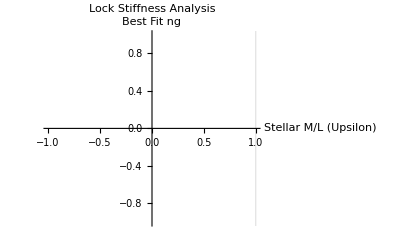

```mathematica
(*Sensitivity of ng to Stellar Mass-to-Light Ratio (Upsilon)*)sensitivityTable=Table[Module[{bestNg},(*Adjust vDisk by a factor of Sqrt[Upsilon]*)vPredictAdj[pt_,ng_]:=ng*Sqrt[pt["vGas"]^2+ups*pt["vDisk"]^2+pt["vBulge"]^2];
(*Find best ng for this specific Upsilon*)tempCost[ng_]:=Total[Table[(pt["vObs"]-vPredictAdj[pt,ng])^2/pt["errV"]^2,{pt,Flatten[Values[galaxyStore],1]}]];
bestNg=n/. Last[FindMinimum[tempCost[n],{n,1.15}]];
{ups,bestNg}],{ups,0.5,1.5,0.1} (*Scan Upsilon from 0.5 to 1.5*)];

ListLinePlot[sensitivityTable,AxesLabel->{"Stellar M/L (Upsilon)","Best Fit ng"},PlotLabel->"Lock Stiffness Analysis",GridLines->{{1.0},{1.1547}},PlotStyle->Thick]
```

```mathematica
(*Generate Residuals for all galaxies at the Theoretical Lock*)allResiduals=Flatten[Table[Table[{pt["R"],pt["vObs"]-vPredict[pt,ngTheoretical]},{pt,galData}],{galData,Values[galaxyStore]}],1];

ListPlot[allResiduals,AxesLabel->{"Radius (kpc)","Velocity Residual (km/s)"},PlotLabel->"Residual Flatness (ng = 1.1547)",PlotRange->All,Filling->Axis,PlotStyle->PointSize[Medium]]
```

-Graphics-